1. Clear memory, load packages and physical constants.

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Needs["Developer`"];
nd=NotebookDirectory[];
CloseKernels[];
LaunchKernels[];
FLASHv=4;
G=If[FLASHv==3,6.6725985×10^-8,6.67428×10^-8];
au=1.49598×10^13;
msun=1.9889225×10^33;
mjup=1.89813×10^30;
rjup=7.1492*10^9;
rearth=6.3781*10^8;
mearth=5.97219*10^27;
Å=10^-8;
yr=3.1556926×10^7;
month=yr/12;
day=86400;
c=2.99792458×10^10;
h=6.626068×10^-27;
kb=1.3806503×10^-16;
pc=3.08568025×10^18;
eV=1.60217646×10^-12;
keV=10^3 eV;
σb=5.6704×10^-5;
σt=6.6524586×10^-25;
mp=1.67262158×10^-24;
arad=4σb/c;
Jsun=1.95×10^48;
rsun=6.955×10^10;
Isun=Jsun/(2π/(27×86400));
Lsun=3.839×10^33;
Mpc=3.08568025×10^24;
k=1.38×10^-16;
km=10^5;
Ωl=0.73;
Ωm=0.27;
ℋ0=70km;
τℋ=1.3*10^10 yr;
```

2. Run the dark year calculations (unless loading from an old run, in which case skip to cell 2B).

```mathematica
make3Dimgs=True;
startype="HWD";
nexamples=16(*1*);
ars={1.0001};
maxnellipses=30;
ellipsepoints=400;
ellipse3dpoints=40;
eps=10^-6;
mine=0.5;

usefixed=False;
usefixedaspin=False;
fixedβ=1.;
fixedaspin=0.9;
fixedmh=10^7.0;
fixedms=1.;
fixedϕ=0*π/2;

(*fsuffix="-MS-compare";*)
fsuffix="-H-WDs";

(*Everything below this line should remain unchanged*)
dell=(1-2eps)/(ellipsepoints/2);
ellipseθs=2.ArcCos[Join[Range[1-eps,eps,-dell],Range[-eps,-1+eps,-dell]]];
ellipsef[e_?NumericQ]:=Module[{},
Table[{(rp Cos[θ])/(1+e Cos[θ])(1+e),(rp Sin[θ])/(1+e Cos[θ])(1+e),0,-Sin[θ]/(√(rp(1+e))),(e+Cos[θ])/(√(rp(1+e))),0},{θ,ellipseθs}]
];
ellipsef2={(rp Cos[θ])/(1+e Cos[θ])(1+e),(rp Sin[θ])/(1+e Cos[θ])(1+e),0,-Sin[θ]/(√(rp(1+e))),(e+Cos[θ])/(√(rp(1+e))),0};
ellipser[tubepts_,radmult_?NumericQ]:=Module[{radii},
radii=Norm/@tubepts;
radii*=q^(-1/3);
radii*=radmult
];
ellipser2[x_,radmult_]:=q^(-1/3)radmult Norm@x;
(*ellipseg[tubepts_,radii_,vc_,sc_:True]:=Module[{},
Tube[BezierCurve[tubepts,SplineDegree->1,SplineClosed->sc],radii,VertexColors->vc]
];*)
ellipseg[tubepts_,radii_,vc_,mode_:0]:=Module[{},
If[mode==0,Tube[tubepts,radii,VertexColors->vc],Line[tubepts]]
];
βpdf=ββ^-2;
kwdf=Exp[-1/2((m-0.6)/0.2)^2];
kf = Piecewise[{{m^(-0.3), 0.01 < m < 0.08},{1/(0.08^0.3*(m/0.08)^1.3), 0.08≤ m<0.5}},1/(0.08^0.3*(0.5/0.08)^1.3*(m/0.5)^2.3)]; 
lmmin=0.1; lmmax=100;
mmspdf= ProbabilityDistribution[kf/NIntegrate[kf, {m,lmmin,0.08,0.5,lmmax}], {m,lmmin,lmmax}];
mwdmin=0.15; mwdmax=1.43;
mwdpdf= ProbabilityDistribution[kwdf/NIntegrate[kwdf, {m,mwdmin,mwdmax}], {m,mwdmin,mwdmax}];
RMs=Compile[{{Msdes,_Real}},With[{M=Max[0.1,Msdes]},(1.715359 M^2.5+6.597788 M^6.5+10.08855 M^11+1.012495 M^19+0.07490166 M^19.5)/(0.01077422+3.082234 M^2+17.84778 M^8.5+M^18.5+0.00022582 M^19.5)],RuntimeAttributes->{Listable}];(*Tout 1996*)
RWD=Compile[{{Msdes,_Real}},0.0112 √((Msdes/1.433)^(-2/3)-(Msdes/1.433)^(2/3)),RuntimeAttributes->{Listable}];

Piecewise[{
{RStar=RMs;
mpdf=mmspdf;
lmhmin=5;
lmhmax=8;
βmin=0.5;
,startype=="MS"},
{RStar=RWD;
mpdf=mwdpdf;
lmhmin=2;
lmhmax=Log10[((mwdmin^(-1/3)RStar[mwdmin] rsun c^2)/(G msun βmin))^(3/2)];
βmin=0.5;
,startype=="WD"},
{RStar=(0.267&);
mpdf=UniformDistribution[{0.171,0.17100001}];
lmhmin=2;
lmhmax=Log10[((mwdmin^(-1/3)RStar[mwdmin] rsun c^2)/(G msun βmin))^(3/2)];
βmin=1.0;
,startype=="HWD"}
}]

makeCircle[cent_,rad_,pts_:20]:=Module[{θ},Table[cent+rad{Cos[θ],Sin[θ]},{θ,0,2π-2π/pts,2π/pts}]];
makeCircle3D[cent_,rad_,pts_:20]:=Module[{θ},Table[cent+rad{Cos[θ],Sin[θ],0},{θ,0,2π-2π/pts,2π/pts}]];
shortestPolygonPath[points_,opts:OptionsPattern[FindShortestTour]]:=Module[{distanceFunction=If[#===Automatic,EuclideanDistance,#]&[OptionValue[DistanceFunction]],magicPoint,d},d[args__]/;FreeQ[{args},magicPoint]:=distanceFunction[args];
d[__]=0;
FindShortestTour[Append[points,magicPoint],DistanceFunction->d,opts]/.{l:{__Integer}:>Most@RotateLeft[l,Position[l,1+Length@points,1,1][[1,1]]]}];
makeHammer[points_]:=Module[{hammerx,hammery},
hammerx=(2 √2 Cos[points⟦All,2⟧]Sin[points⟦All,1⟧/2])/(√(1+Cos[points⟦All,2⟧]Cos[points⟦All,1⟧/2]));
hammery=(√2 Sin[points⟦All,2⟧])/(√(1+Cos[points⟦All,2⟧]Cos[points⟦All,1⟧/2]));
{hammerx,hammery}ᵀ];
(*Extra factor of e below comes from slight difference in periapse of different ellipses. Second De-Sitter term comes from expanding angular frequency, Subscript[ω, p]=√(1-3(Subscript[r, s]^2 c^2)/h^2)*)
Ωaps:=frac((*With[{co=(G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))},6π co+27π co^2+189π co^3+(6237π/4) co^4]*)(6π G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))(*With[{arg=(12 G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))},If[arg<1,2π(1-(1-arg)^(1/4)),2π arg(*Gross approximation*)]]*)-Cos[𝒾](12π aspin)/(c^3 q^(1/2))((β G mh msun)/(rs rsun e(1+e)))^(3/2)+(3π aspin^2)/(2 c^4)((G mh msun β)/((1+e)q^(1/3)rs rsun e))^2(1-5 Cos[𝒾]^2));(*Merritt book 2013*)
Ωnod:=frac((4π aspin)/(c^3 q^(1/2))((β G mh msun)/(rs rsun e(1+e)))^(3/2)+(3π aspin^2)/c^4((G mh msun β)/((1+e)q^(1/3)rs rsun e))^2 Cos[𝒾]);
rotationtransform[ee_?NumericQ,𝒾𝒾_?NumericQ,zax_?VectorQ,yax_?VectorQ,ff:(_?NumericQ):1]:=Block[{e=ee,𝒾=𝒾𝒾,frac=ff},Composition@@{RotationTransform[(*(1+Ωaps/(2π))*)Ωnod,RotationTransform[(*(1+Ωaps/(2π))*)Ωaps,zax][spindir]],RotationTransform[(*(1+Ωaps/(2π))*)Ωaps,zax]}];
ecc0=1-q^(-1/3)Max[β,1];
a0=rp/(1-ecc0);
newJ=aspins=βs=qs=mhs=mss=rss=ratereduce=circorbs=circcollind=ConstantArray[0,nexamples];
collidingstreams=spindirs=ConstantArray[{},nexamples];
collisioninfo=ConstantArray[{},nexamples];
norbs=sellipsepts=sellipseradii=θmap=sellipsefuncs=srotationtransforms=seccs=sbsfs=ConstantArray[{},nexamples];
footpointpls=ConstantArray[{},{nexamples,maxnellipses}];

Off[FindRoot::reged];
ParallelEvaluate[Off[FindRoot::reged]];

progresscount=0;
starttime=curtime=AbsoluteTime[];

SetSharedVariable[progresscount,sellipsefuncs,θmap,circcollind,circorbs,ratereduce,newJ,footpointpls,collidingstreams,collisioninfo,norbs,
sellipsepts,sellipseradii,srotationtransforms,seccs,sbsfs,spindirs,aspins,βs,qs,mhs,mss,rss,progresscount,curtime];

Monitor[ParallelDo[
foundcombo=False;
While[!foundcombo,
If[usefixed,
mhs⟦n⟧=fixedmh;,
mhs⟦n⟧=10^RandomReal[{lmhmin,lmhmax}];
];

mh=mhs⟦n⟧;
maxβ=0;
trycount=0;
While[maxβ<βmin,
If[trycount≥100,
(*Print["Too many tries, M_h = ",mh];*)
Break[];
];
If[usefixed||usefixedaspin,
aspins⟦n⟧=fixedaspin;
,
aspins⟦n⟧=RandomReal[];
];
If[usefixed,
mss⟦n⟧=fixedms;
spindirs⟦n⟧=Normalize@{Cos[fixedϕ],0,Sin[fixedϕ]};
,
mss⟦n⟧=RandomVariate[mpdf];
spindirs⟦n⟧=Normalize@RandomVariate[NormalDistribution[],3];
];
ms=mss⟦n⟧;
rss⟦n⟧=RStar[ms];
rs=rss⟦n⟧;
aspin=aspins⟦n⟧;
spindir=spindirs⟦n⟧;
angfac=Sin@ArcTan[Norm@spindir⟦;;2⟧,spindir⟦3⟧];
rbs=2-angfac aspin+2 √(1-angfac aspin);
qs⟦n⟧=mh/ms;
q=qs⟦n⟧;
If[q^(1/3)(1-mine)<1,maxβ=0];(*Cycle out of this*)
(*Currently restrict orbits to lie outside ISCO, but IBCO orbits should be included.*)
maxβ=Min[q^(1/3)(1-mine),(q^(1/3)rs rsun c^2)/(rbs G mh msun)(*With[{e=1},(q^(1/3)rs rsun c^2 e(1+e))/(12 G mh msun)]*)];
If[maxβ<βmin&&usefixed,Print["Error: Bad fixed parameters."];Return[];];
trycount++;
];
If[maxβ≥βmin,foundcombo=True;];
];
ratereduce⟦n⟧=1.0/trycount;
If[usefixed,
βs⟦n⟧=fixedβ;,
βpdfnorm=NIntegrate[βpdf,{ββ,βmin,maxβ}];
βpd=ProbabilityDistribution[βpdf/βpdfnorm,{ββ,βmin,maxβ}];
βs⟦n⟧=RandomVariate[βpd];
];
β=βs⟦n⟧;
rp=1/β;
Do[
newtransform=rotationtransform[1,ArcCos[Dot[{0,0,1},spindir]],{0,0,1},{0,1,0},0.5];
relis={ArcCos[Dot[newtransform[{0,0,1}],spindir]]};
rotationtransforms={newtransform};
zaxes={newtransform[{0,0,1}]};
yaxes={newtransform[{0,1,0}]};

scales=Reverse[Range[nellipses]^(2/3)];
eccs=1-rp/(a0 scales);

(*relis={ArcCos[Dot[{0,0,1},spindir]](*-π/2*)};*)
(*rotationtransforms={RotationTransform[0,{0,0,1}]};*)

Do[
newtransform=rotationtransform[eccs⟦i-1⟧,relis⟦i-1⟧,zaxes⟦i-1⟧,yaxes⟦i-1⟧];
comptransform=Composition[rotationtransform[eccs⟦i-1⟧,relis⟦i-1⟧,zaxes⟦i-1⟧,yaxes⟦i-1⟧],rotationtransforms⟦i-1⟧];
newreli=(ArcCos[Dot[rotationtransforms⟦i-1⟧[{0,0,1}],spindir]](*-π/2*));
AppendTo[relis,newreli];
AppendTo[rotationtransforms,comptransform];
AppendTo[zaxes,newtransform[zaxes⟦i-1⟧]];
AppendTo[yaxes,newtransform[yaxes⟦i-1⟧]];
(*newreli=(ArcCos[Dot[(Composition@@Reverse@rotationtransforms⟦;;i-1⟧)[{0,0,1}],spindir]]-π/2);*)
,{i,2,nellipses}];

ellipsefuncs=FullSimplify[#,Assumptions->{0≤θ≤2π}]&/@Table[Join[rotationtransforms⟦i⟧[((ellipsef2/.e->eccs⟦i⟧)⟦;;3⟧)],rotationtransforms⟦i⟧[((ellipsef2/.e->eccs⟦i⟧)⟦4;;⟧)]],{i,nellipses}];
ellipseradius=Reverse@Table[((rp(1+e))/(1+e Cos[θ])q^(-1/3)β(nellipses-i+1))/.e->eccs⟦i⟧,{i,nellipses}];

lcollidingstreams={};
If[nellipses>1,
dists=Map[(Function[{a,b},{{a,b},NMinimize[{Block[{bsxf1=ellipsefuncs⟦a,;;3⟧/.θ->2π x,bsxf2=ellipsefuncs⟦b,;;3⟧/.θ->2π y,r1=ellipseradius⟦a⟧/.θ->2π x,r2=ellipseradius⟦b⟧/.θ->2π y,bsvf1=ellipsefuncs⟦a,4;;⟧/.θ->2π x,bsvf2=ellipsefuncs⟦b,4;;⟧/.θ->2π y},Log[(1+(Norm[bsxf1-bsxf2]-(r1+r2))/(r1+r2))Sin[1/2 ArcCos[(bsvf1.bsvf2)/(Norm@bsvf1 Norm@bsvf2)]]^-2(*(2/(Norm[bsxf1]+Norm[bsxf2]))^-1 y*)]],If[a==1,1/2,0.0001]<x<1,If[b==1,1/2,0.0001]<y<1},{x,y},MaxIterations->1000,AccuracyGoal->∞,PrecisionGoal->6,Method->{"SimulatedAnnealing"}]}]@@#&),
Select[Subsets[Range@nellipses,{2}],(*Abs[#⟦1⟧-#⟦2⟧]>1&&*)True&]];

lcollidingstreams=Sort[Select[Sort[dists,#1⟦2,1⟧<#2⟦2,1⟧&],Function[{z},(*x⟦2,1⟧*)
Block[{a=z⟦1,1⟧,b=z⟦1,2⟧,xx=x/.z⟦2,2⟧,yy=y/.z⟦2,2⟧,bsxf1,bsxf2,r1,r2},
bsxf1=ellipsefuncs⟦a,;;3⟧/.θ->2π xx;
bsxf2=ellipsefuncs⟦b,;;3⟧/.θ->2π yy;
r1=ellipseradius⟦a⟧/.θ->2π xx;
r2=ellipseradius⟦b⟧/.θ->2π yy;
Norm[bsxf1-bsxf2]-(r1+r2)<0]]],Max@#1⟦1⟧<Max@#2⟦1⟧&];
];

norbs⟦n⟧=nellipses;

If[Length@lcollidingstreams>0,
θs=Sort/@(Reap[Table[Module[{pp},pp=ParametricPlot3D[ellipsefuncs⟦m,;;3⟧,{θ,If[m==1,π,0],2π},PlotRange->All,EvaluationMonitor:> Sow[θ,m],PlotPoints->40,MaxRecursion->10];Cases[pp,Line[x_]:>x,-1]⟦1⟧],{m,nellipses}]]⟦2⟧);
θmap⟦n⟧=Table[Interpolation[{θi,Range@Length@θi}ᵀ,InterpolationOrder->0],{θi,θs}];
sellipsefuncs⟦n⟧=ellipsefuncs;
sellipsepts⟦n⟧=Table[Map[(Table[#/.θ->θθ,{θθ,θs⟦m⟧}])&,ellipsefuncs⟦m⟧,{-1}],{m,nellipses}];
sellipsepts⟦n⟧=Table[Transpose@sellipsepts⟦n,m⟧,{m,nellipses}];
sellipseradii⟦n⟧=Table[Map[(Table[#/.θ->θθ,{θθ,θs⟦m⟧}])&,ellipseradius⟦m⟧,{-1}],{m,nellipses}];
srotationtransforms⟦n⟧=rotationtransforms;

(*sellipsepts⟦n⟧=Re@Table[Join[rotationtransforms⟦i⟧/@(ellipsef[eccs⟦i⟧]⟦All,;;3⟧),rotationtransforms⟦i⟧/@(ellipsef[eccs⟦i⟧]⟦All,4;;⟧),2],{i,nellipses}];
sellipseradii⟦n⟧=Reverse@Table[ellipser[sellipsepts⟦n,i,All,;;3⟧,β(nellipses-i+1)],{i,nellipses}];*)

seccs⟦n⟧=eccs;
bsf[u_?NumericQ,i_?IntegerQ]:=Norm[ellipsefuncs⟦i,;;3⟧/.θ->2π u];

impangle[s1_,s2_,x1_,x2_]:=Module[{a=ellipsefuncs⟦s1,4;;⟧/.θ->2π x1,b=ellipsefuncs⟦s2,4;;⟧/.θ->2π x2},Max[Min[1,(a.b)/(Norm@a Norm@b)],-1]];
circorb=Min[Max/@lcollidingstreams⟦All,1⟧];
orbstocheck=Flatten@Position[lcollidingstreams⟦All,1⟧,x_/;Max@x==circorb,{1},Heads->False];

collidingstreams⟦n⟧=lcollidingstreams;
circorbs⟦n⟧=circorb;
circcollind⟦n⟧=orbstocheck⟦Ordering[y/.lcollidingstreams⟦orbstocheck,2,2⟧,1]⟦1⟧⟧;
collisioninfo⟦n⟧=Table[{180/π ArcCos@impangle[lcollidingstreams⟦i,1,1⟧,lcollidingstreams⟦i,1,2⟧,x/.lcollidingstreams⟦i,2,2⟧,y/.lcollidingstreams⟦i,2,2⟧],bsf[x/.lcollidingstreams⟦i,2,2⟧,lcollidingstreams⟦i,1,1⟧]},{i,Length@lcollidingstreams}];

Break[]];
,{nellipses,1,maxnellipses}];
progresscount++;
(*curtime=AbsoluteTime[];*)
,{n,nexamples}],
Refresh[Pause[0.03];Row[{ProgressIndicator[progresscount,{0,nexamples}],ToString@NumberForm[progresscount/nexamples 100.,{4,2}]<>"%, time remaining: ",DateDifference[0,(AbsoluteTime[]-starttime)/(progresscount+1)(nexamples-progresscount),{"Hour","Minute","Second"}]}," "],TrackedSymbols->{},UpdateInterval->1]];
```

2A. Dump the data from the run above to disk. Note that this will overwrite any dumps with the same suffix.

```mathematica
DumpSave[nd<>"dark-year"<>fsuffix<>".mx","Global`"];
```

2B. Load the data from a run into memory. If running this cell, you can skip running cells 1-2A.

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Needs["Developer`"];
Get[NotebookDirectory[]<>"dark-year-WD.mx"]
nd=NotebookDirectory[];
```

3. Define a function that will render images of a given realization from the simulation above.

```mathematica
Options[makestreamimage]={ImageSize->1000,UseExactSolution->False,ShowSpinArrow->True,Zoom->1,XClip->{-1,1},YClip->1,ZClip->1};
makestreamimage[n_?IntegerQ,mode_?IntegerQ,OptionsPattern[]]:=Module[{collstlist,maxorbs,collpoints,collloc,colswitch,risc,ellipses},
collstlist=Union@Flatten@collidingstreams⟦n,All,1⟧;
maxorbs=circorbs⟦n⟧;
collpoints=(sellipsefuncs⟦n,#⟦1⟧⟧/.θ->2π#⟦2⟧&/@({collidingstreams⟦n,All,1,2⟧,collidingstreams⟦n,All,2,2,2,2⟧}ᵀ))⟦All,;;3⟧;
(*collloc=Position[Max/@collidingstreams⟦n,All,1⟧,x_/;x==maxorbs]⟦1,1⟧;*)
collloc=circcollind⟦n⟧;
colswitch[i_?IntegerQ]:=If[mode==1,Black,If[MemberQ[collstlist,i],Orange,Blue]];
risc=((2-aspins⟦n⟧+2 √(1-aspins⟦n⟧)) G mhs⟦n⟧ msun)/(qs⟦n⟧^(1/3)c^2 rss⟦n⟧ rsun Norm[spindirs⟦n⟧]);

ellipses=Join[{Lighting->"Neutral"},If[mode==0,Join[{Opacity@0.5,Green},Flatten[{Sphere[#,2sellipseradii⟦n,maxorbs,Nearest[sellipsepts⟦n,maxorbs,All,;;3⟧->Automatic,collpoints⟦collloc⟧]⟦1⟧⟧]}&/@collpoints⟦{collloc}⟧]],{}],
{Darker@Gray,Opacity@0.5,Sphere[{0,0,0},risc],Darker@Gray,CapForm["Butt"],AbsoluteThickness@4,Opacity@1},If[OptionValue@ShowSpinArrow,{Arrowheads[0.03],Arrow[Tube[{{0,0,0},0.5spindirs⟦n⟧Norm[collpoints⟦collloc⟧]},0.01Norm[collpoints⟦collloc⟧]]]},{}],
Flatten[Join[{CapForm["Round"],JoinForm["None"]},If[mode==1,{Black,AbsoluteDashing[{8,6}]},{}],{
ellipseg[
Flatten[Riffle[Table[Block[{arr,len=Length[sellipsepts⟦n,i⟧]},arr=sellipsepts⟦n,i,Range[1,If[i==maxorbs,Max[1,Floor[θmap⟦n,i⟧[2π(y/.collidingstreams⟦n,collloc,2,2⟧)]]-1],len]],;;3⟧;If[i==maxorbs,arr~Join~{collpoints⟦collloc⟧},arr]],{i,maxorbs}],Table[Block[{vec,len=Length[sellipsepts⟦n,i⟧]},vec=(ncon-1-j)/(ncon-1) sellipsepts⟦n,i,len,;;3⟧Norm[sellipsepts⟦n,i+1,1,;;3⟧]+
j/(ncon-1)sellipsepts⟦n,i+1,1,;;3⟧Norm[sellipsepts⟦n,i,len,;;3⟧];
(vec/Norm[vec])((ncon-1-j)/(ncon-1)  Norm[sellipsepts⟦n,i+1,1,;;3⟧]+j/(ncon-1)Norm[sellipsepts⟦n,i,len,;;3⟧])],
{i,maxorbs-1},{j,0,ncon-1}]],1],
Flatten[Riffle[Table[Block[{arr,len=Length[sellipsepts⟦n,i⟧]},arr=sellipseradii⟦n,i,Range[1,If[i==maxorbs,Max[1,Floor[θmap⟦n,i⟧[2π(y/.collidingstreams⟦n,collloc,2,2⟧)]]-1],len]]⟧;
If[i==maxorbs,arr~Join~{sellipseradii⟦n,maxorbs,Nearest[sellipsepts⟦n,maxorbs,All,;;3⟧->Automatic,collpoints⟦collloc⟧]⟦1⟧⟧},arr]],{i,maxorbs}],Table[Block[{len=Length[sellipsepts⟦n,i⟧]},((ncon-1-j)/(ncon-1) sellipseradii⟦n,i,len⟧+j/(ncon-1)sellipseradii⟦n,i+1,1⟧)],{i,maxorbs-1},{j,0,ncon-1}]]],
Flatten[Table[Block[{arr,len=Length[sellipsepts⟦n,i⟧]},arr=ConstantArray[colswitch@i,len];If[i<maxorbs,arr~Join~Table[Directive[Opacity@0.5,Blend[{colswitch@i,colswitch[i+1]},j/(ncon-1)]],{j,0,ncon-1}],arr]],{i,maxorbs}]],
mode]}],1]];
exactsolpl=If[OptionValue[UseExactSolution],
(*finalrot=RotationMatrix[{{1,0,0},Block[{i=1},Block[{spindir=spindirs⟦i⟧,aspin=aspins⟦i⟧,q=qs⟦i⟧,rs=rss⟦i⟧,ms=mss⟦i⟧,mh=mhs⟦i⟧,β=βs⟦i⟧},rotationtransform[1,ArcCos[Dot[{0,0,1},spindir]]-π/2,{0,0,1},{0,1,0},-0.5][{1,0,0}]]]}];*)
Graphics3D[{AbsoluteThickness@4,Red,Line[((G mhs⟦n⟧msun βs⟦n⟧)/(c^2 rss⟦n⟧rsun qs⟦n⟧^(1/3)) )(*finalrot.#&/@*)exactsol]},PlotRange->All]
,
Graphics3D[{}]];
Show[Graphics3D[ellipses],exactsolpl,ImageSize->{Automatic,OptionValue[ImageSize]},Boxed->False,PlotRange->(1.5/OptionValue[Zoom])Norm[collpoints⟦collloc⟧]{OptionValue[XClip],OptionValue[YClip]{-1,1},OptionValue[ZClip]{-1,1}},ViewPoint->{0,0,100}]]
```

4. Export images of all realizations from the simulation above to a folder. Requires cell 3. to have been evaulated.

```mathematica
ParallelDo[
ellipsespl=makestreamimage@n;
UsingFrontEnd@Export[nd<>"examples/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png",ellipsespl];
,{n,(*{188,  508, 151, 58, 427, 644, 723}*)400(*nexamples*)}];
```

5. Determine times of peak and accretion rate at peak. Will likely generate a lot of warnings if number of realizations is small.

```mathematica
(*
αhr2 determines the ratio of the orbital period of the most-bound debris to the circularization time. Value here is set by hand but likely does depend on conditions in the stream-stream collision location, a place for potential improvement.
*)
αhr2=100;

Get[nd<>"CustomTicks.m"];
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;
tmb=2π √(((1/2 qs^(2/3)rss rsun/(Max[#,1]&/@βs))^3)/(G mhs msun));
typems[m_?NumericQ]:=If[m>0.3&&m<2,2,1];
tpeakco[type_?NumericQ,ββ_?NumericQ]:=Module[{β},If[type==1,
β=Min[2.5,Max[0.5,ββ]];(-0.30908+1.1804 √β-1.1764β)/(1+1.3089 √β-4.1940β),
β=Min[4,Max[0.6,ββ]];(-0.3867+0.57291 √β-0.31231β)/(1-1.2744 √β-0.90053β)]];
mpeakco[type_?NumericQ,ββ_?NumericQ]:=Module[{β},Exp[If[type==1,
β=Min[2.5,ββ];(10.253-17.380β+5.9988 β^2)/(1-0.46573β-4.5066 β^2),
β=Min[4,ββ];(27.261-27.516β+3.8716 β^2)/(1-3.2605β-1.3865 β^2)]]];
tpeakms[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=tpeakco[typems[ms],β] (mh/10^6)^(1/2)ms^-1 RMs[ms]^(3/2);
mpeakms[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=mpeakco[typems[ms],β](mh/10^6)^(-1/2)ms^2 RMs[ms]^(-3/2);
tpeakwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=tpeakco[If[ms>1,2,1],β] (mh/10^6)^(1/2)ms^-1 RWD[ms]^(3/2);
mpeakwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=mpeakco[If[ms>1,2,1],β](mh/10^6)^(-1/2)ms^2 RWD[ms]^(-3/2);
(*From Jamie's HWD sims*)
hwddat=Import[NotebookDirectory[]<>"log_tpeak_log_mdotpeak.dat"];
hwdtpeakf=Interpolation[{hwddat⟦1⟧,hwddat⟦2⟧}ᵀ];
hwdmpeakf=Interpolation[{hwddat⟦1⟧,hwddat⟦3⟧}ᵀ];
tpeakhwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=10^hwdtpeakf[Min[β,10]]/yr(mh/10^6)^(1/2);
mpeakhwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=10^hwdmpeakf[Min[β,10]]yr/msun(mh/10^6)^(-1/2);

tpeak=Switch[startype,"WD",tpeakwd,"MS",tpeakms,"HWD",tpeakhwd];
mpeak=Switch[startype,"WD",mpeakwd,"MS",mpeakms,"HWD",mpeakhwd];
(*circtime=circorbs tmb/(((Min[#,0.9999]&)/@(1/(collisioninfo⟦All,1,2⟧ βs)))2 Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^2);*)

trimcollinfo=Table[collisioninfo⟦n,circcollind⟦n⟧⟧,{n,nexamples}];
eorb=(1/(trimcollinfo⟦All,2⟧ (*βs*)))2 Sin[Min[#,π/2]&/@(0.5Re@trimcollinfo⟦All,1⟧°)]^2 G mhs msun/(2 qs^(1/3)rss rsun/βs);
circtime=αhr2(*Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^-4*)π/(√2) G mhs msun eorb^(-3/2);
fillingtime=2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))(12^(1/3)qs^(1/9))/βs^(2/3);(*2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))qs^(1/3);*)
circtime=Min[#⟦1⟧,#⟦2⟧]&/@({circtime,fillingtime}ᵀ);
peaktime=((tpeak@@#)yr&)/@({βs,mss,mhs}ᵀ);
delaytime=tmb Max/@collidingstreams⟦All,1,1,{1,2}⟧(*+circtime*);
delaydat={Log10@mhs,Log10[delaytime/yr]}ᵀ;
circratio=circtime/peaktime;
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {$Failed⟦1⟧,$Failed⟦2⟧} cannot be transposed.

Interpolation::innd: First argument in Transpose[{$Failed⟦1⟧,$Failed⟦2⟧}] does not contain a list of data and coordinates.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {$Failed⟦1⟧,$Failed⟦3⟧} cannot be transposed.

Interpolation::innd: First argument in Transpose[{$Failed⟦1⟧,$Failed⟦3⟧}] does not contain a list of data and coordinates.

6. Plot t_peak and (ṁ)_peak in rough form.

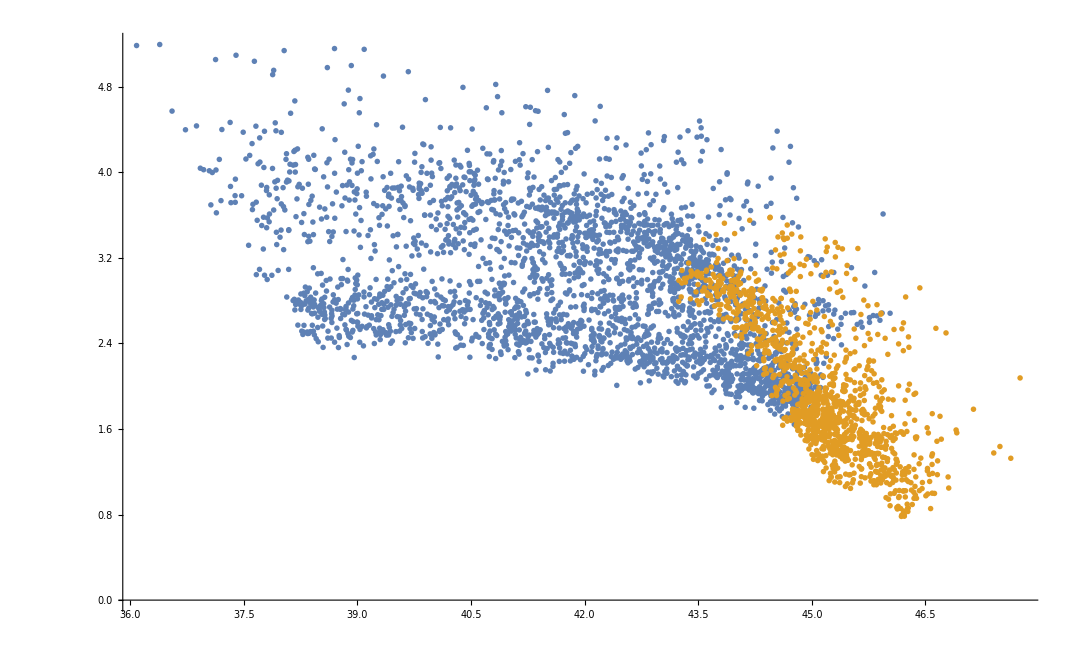

```mathematica
mpeaks=(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ));
subpos=Position[mpeaks/medds,x_/;x<1];
suppos=Position[mpeaks/medds,x_/;x≥1];
lpeaks=Log10[(ϵacc/.a->aspins)c^2 mpeaks msun/yr];
tpeaks=Log10[(Max[#,1]&/@circratio)((tpeak@@#&)/@({βs,mss,mhs}ᵀ))yr/day];
lpeakssub=Extract[lpeaks,subpos];
tpeakssub=Extract[tpeaks,subpos];
subweights=((10^lpeakssub rsun)/((8 G Extract[mhs,subpos]((tpeakssub day)/π)^2)^(2/3)))^(3/4);
subweights/=Max@subweights;
lpeakssup=Extract[lpeaks,suppos];
tpeakssup=Extract[tpeaks,suppos];
supweights=(10^lpeakssup)^(3/2);
supweights/=Max@supweights;
ListPlot[{{lpeakssub,tpeakssub}ᵀ,{lpeakssup,tpeakssup}ᵀ}]
```

7. Plot histograms of the above, separated into sub/super-Eddington.

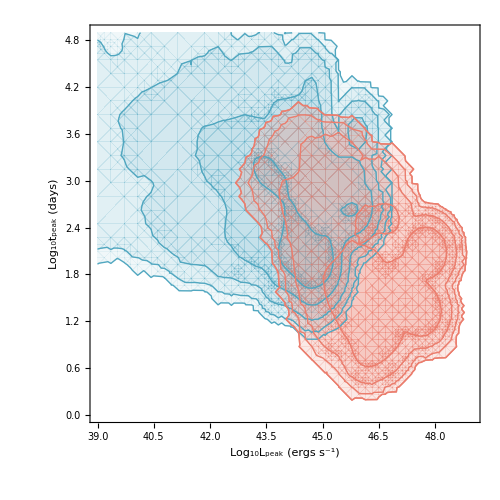
-Graphics- | -Graphics-
-Graphics- |

```mathematica
ci=24;cd1=5;cd2=1;
cd=ColorData[ci,"ColorList"];
nconts=5;

ranges={{39,49},{0,4.9}};

subcolor=cd⟦cd1⟧;
wd=WeightedData[{lpeakssub,tpeakssub}ᵀ,subweights];
skd=KernelMixtureDistribution[wd,MaxMixtureKernels->All];
pskd=PDF[skd,{l,t}];
(*ranges=pskd⟦2,0,1⟧+0.5{{-1,1},{-1,1}};*)
accumarr=Sort[{subweights,subweights}ᵀ,#1⟦1⟧>#2⟦1⟧&];
accumarr⟦All,1⟧=Accumulate[accumarr⟦All,1⟧];
accumarr⟦All,1⟧/=Max[accumarr⟦All,1⟧];
conts=Table[accumarr⟦Nearest[accumarr⟦All,1⟧->Range@Length@subpos,1-2Erfc[s]]⟦1⟧,2⟧,{s,nconts}];
subargs={pskd,{l}~Join~ranges⟦1⟧,{t}~Join~ranges⟦2⟧,PlotRange->All,Contours->conts,Method->{"TransparentPolygonMesh"->True},ClippingStyle->{None,Directive[Opacity[0.5],cd⟦cd1⟧]}};
subfillpl=ContourPlot@@Join[subargs,{ContourStyle->None,ContourShading->Table[Directive[Opacity[0.5 i/(nconts+1)],cd⟦cd1⟧],{i,0,nconts+1}]}];
subcontspl=ContourPlot@@Join[subargs,{ContourStyle->cd⟦cd1⟧,ContourShading->None}];

supcolor=cd⟦cd2⟧;
wd=WeightedData[{lpeakssup,tpeakssup}ᵀ,supweights];
skd=KernelMixtureDistribution[wd,MaxMixtureKernels->All];
pskd=PDF[skd,{l,t}];
(*ranges=pskd⟦2,0,1⟧+0.5{{-1,1},{-1,1}};*)
accumarr=Sort[{supweights,supweights}ᵀ,#1⟦1⟧>#2⟦1⟧&];
accumarr⟦All,1⟧=Accumulate[accumarr⟦All,1⟧];
accumarr⟦All,1⟧/=Max[accumarr⟦All,1⟧];
conts=Table[accumarr⟦Nearest[accumarr⟦All,1⟧->Range@Length@suppos,1-2Erfc[s]]⟦1⟧,2⟧,{s,nconts}];
supargs={pskd,{l}~Join~ranges⟦1⟧,{t}~Join~ranges⟦2⟧,PlotRange->All,Contours->conts,Method->{"TransparentPolygonMesh"->True},ClippingStyle->{None,Directive[Opacity[0.5],cd⟦cd2⟧]}};
supfillpl=ContourPlot@@Join[supargs,{ContourStyle->None,ContourShading->Table[Directive[Opacity[0.5 i/(nconts+1)],cd⟦cd2⟧],{i,0,nconts+1}]}];
supcontspl=ContourPlot@@Join[supargs,{ContourStyle->cd⟦cd2⟧,ContourShading->None}];

hlsub=HistogramDistribution[WeightedData[lpeakssub,subweights],ranges⟦1⟧~Join~{0.5}];hlsup=HistogramDistribution[WeightedData[lpeakssup,supweights],ranges⟦1⟧~Join~{0.5}];
lhist=Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[hlsub,l],(Length@suppos)/nexamples PDF[hlsup,l]},{l}~Join~ranges⟦1⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,5},{1,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0,0.1}},ImageSize->{500,75},AspectRatio->Full];

htsub=HistogramDistribution[WeightedData[tpeakssub,subweights],ranges⟦2⟧~Join~{0.25}];htsup=HistogramDistribution[WeightedData[tpeakssup,supweights],ranges⟦2⟧~Join~{0.25}];
thist=Rotate[MapAt[Scale[#,{1,-1}]&,Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[htsub,l],(Length@suppos)/nexamples PDF[htsup,l]},{l}~Join~ranges⟦2⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,1},{5,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0.1,0}},ImageSize->{500,75},AspectRatio->Full],{1}],90°];

Grid[{{lhist,thist},{Show[subfillpl,supfillpl,subcontspl,supcontspl,PlotRange->ranges,FrameLabel->{"Log_10L_peak (ergs s^-1)","Log_10t_peak (days)"},FrameStyle->Directive[AbsoluteThickness@1,FontSize->16],ImageSize->{500,500},AspectRatio->Full,ImagePadding->{{50,5},{50,1}}],SpanFromAbove}},Spacings->0,Alignment->{Left,Bottom},Background->White]
```

```mathematica
hlsub=HistogramDistribution[WeightedData[lpeakssub,subweights],ranges⟦1⟧~Join~{0.5}];hlsup=HistogramDistribution[WeightedData[lpeakssup,supweights],ranges⟦1⟧~Join~{0.5}];
lhist=Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[hlsub,l],(Length@suppos)/nexamples PDF[hlsup,l]},{l}~Join~ranges⟦1⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,10},{1,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0,0.1}},ImageSize->500];

htsub=HistogramDistribution[WeightedData[tpeakssub,subweights],ranges⟦2⟧~Join~{0.25}];htsup=HistogramDistribution[WeightedData[tpeakssup,supweights],ranges⟦2⟧~Join~{0.25}];
thist=Rotate[MapAt[Scale[#,{1,-1}]&,Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[htsub,l],(Length@suppos)/nexamples PDF[htsup,l]},{l}~Join~ranges⟦2⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,10},{1,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0.1,0}},ImageSize->500],{1}],90°]
```

-Graphics-

8. Fraction of events that are prompt vs. slowed as a function of (α^-1(h/r))^-2, the macguffin carried over from the previous calculation.

```mathematica
αhr2s=10^Range[0,4,0.1];
abovepromptfracs=aboveaffectfracs=belowpromptfracs=belowaffectfracs=ConstantArray[0,Length@αhr2s];
Do[
αhr2=αhr2s⟦i⟧;
circtime=αhr2(*Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^-4*)π/(√2) G mhs msun eorb^(-3/2);
fillingtime=2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))(12^(1/3)qs^(1/9))/βs^(2/3);(*2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))qs^(1/3);*)
circtime=Min[#⟦1⟧,#⟦2⟧]&/@({circtime,fillingtime}ᵀ);
peaktime=((tpeak@@#)yr&)/@({βs,mss,mhs}ᵀ);
delaytime=tmb Max/@collidingstreams⟦All,1,1,{1,2}⟧(*+circtime*);
delaydat={Log10@mhs,Log10[delaytime/yr]}ᵀ;
circratio=circtime/peaktime;
(*circratio=circtime/(1/2 circorbs (1+circorbs)tmb);*)
spinlimit=0;
mhcut=10^(cc/.myfit);
fastevents=Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[mhs,x_/;x>mhcut,{1},Heads->False]];
slowedevents=Intersection[Position[circratio,x_/;x>1,{1},Heads->False],Position[mhs,x_/;x>mhcut,{1},Heads->False]];
affectedevents=Intersection[Position[circratio,x_/;1>x>1/3,{1},Heads->False],Position[mhs,x_/;x>mhcut,{1},Heads->False]];
numer=Length@fastevents+Length@slowedevents+Length@affectedevents;
abovepromptfracs⟦i⟧=N@((Length@fastevents)/numer);
aboveaffectfracs⟦i⟧=N@((Length@affectedevents)/numer);
fastevents=Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[mhs,x_/;x<mhcut,{1},Heads->False]];
slowedevents=Intersection[Position[circratio,x_/;x>1,{1},Heads->False],Position[mhs,x_/;x<mhcut,{1},Heads->False]];
affectedevents=Intersection[Position[circratio,x_/;1>x>1/3,{1},Heads->False],Position[mhs,x_/;x<mhcut,{1},Heads->False]];
numer=Length@fastevents+Length@slowedevents+Length@affectedevents;
belowpromptfracs⟦i⟧=N@((Length@fastevents)/numer);
belowaffectfracs⟦i⟧=N@((Length@affectedevents)/numer);
,{i,Length@αhr2s}];
```

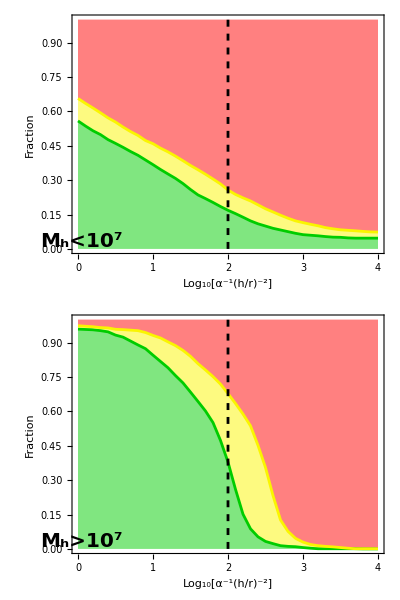

```mathematica
fiducialpl=ListPlot[{{2,0},{2,1}},Joined->True,PlotStyle->Directive[Black,AbsoluteThickness@2,AbsoluteDashing@5]];
viscouspl=Grid[{{Show[ListPlot[{{Log10[αhr2s],belowpromptfracs}ᵀ,{Log10[αhr2s],belowpromptfracs+belowaffectfracs}ᵀ},Joined->True,PlotStyle->(Directive[AbsoluteThickness@2,#]&/@delaycolors),Filling->{{1->{Bottom,Lighter[delaycolors⟦1⟧,0.5]}},{1->{{2},Lighter[delaycolors⟦2⟧,0.5]}},{2->{Top,Lighter[delaycolors⟦3⟧,0.5]}}},Frame->True,ImageSize->400,FrameLabel->{"Log_10[α^-1(h/r)^-2]","Fraction"},Axes->False,PlotRangePadding->0,FrameStyle->Directive[AbsoluteThickness@1,FontSize->16],PlotRange->{All,{0,1}},Epilog->{Inset[Style["M_h<10^7",Bold,FontSize->20,SingleLetterItalics->False],Scaled[{0.03,0.05}],Scaled[{0,0}]]}],fiducialpl]},
{Show[ListPlot[{{Log10[αhr2s],abovepromptfracs}ᵀ,{Log10[αhr2s],abovepromptfracs+aboveaffectfracs}ᵀ},Joined->True,PlotStyle->(Directive[AbsoluteThickness@2,#]&/@delaycolors),Filling->{{1->{Bottom,Lighter[delaycolors⟦1⟧,0.5]}},{1->{{2},Lighter[delaycolors⟦2⟧,0.5]}},{2->{Top,Lighter[delaycolors⟦3⟧,0.5]}}},Frame->True,ImageSize->400,FrameLabel->{"Log_10[α^-1(h/r)^-2]","Fraction"},Axes->False,PlotRangePadding->0,FrameStyle->Directive[AbsoluteThickness@1,FontSize->16],PlotRange->{All,{0,1}},Epilog->{Inset[Style["M_h>10^7",Bold,FontSize->20,SingleLetterItalics->False],Scaled[{0.03,0.05}],Scaled[{0,0}]]}],fiducialpl]
}}]
Export[nd<>"viscous.pdf",viscouspl];
```

9. Plot slowed events on top of original prompt in (ṁ)_peak/t_peakspace, green shows events limited by the Eddington limit.

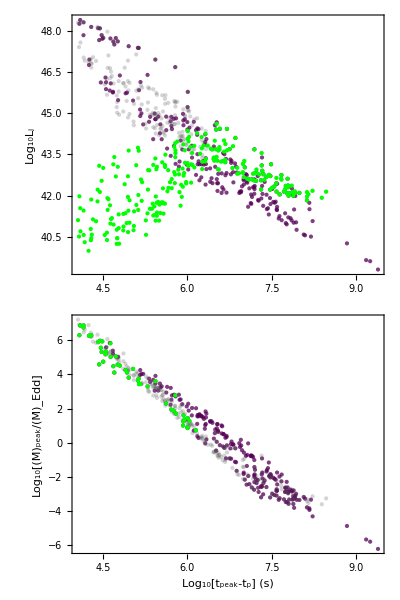

```mathematica
delayconst=1;
wdlpeakpl=ListPlot[{Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ],Log10[{yr(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ],
Log10[{yr(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(Min[mpeak@@#⟦;;3⟧,medd[#⟦3⟧,#⟦4⟧]]&/@({βs,mss,mhs,aspins}ᵀ))}ᵀ](*,Extract[Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ],Position[βs,x_/;x>3]]*)},Axes->False,Frame->True,PlotRange->All,ImageSize->600,FrameStyle->Directive[Black,FontSize->20,AbsoluteThickness@1],FrameLabel->{{Style["Log_10L_j",SingleLetterItalics->False],"Log_10(Ṁ)_peak (M_⊙/yr)"},{Automatic,Automatic}},FrameTicks->{{Automatic,LinTicks[-5,6,2,4,TickPostTransformation->(#+Log10[msun/yr 0.1 c^2]&)]},{Automatic,Automatic}},PlotStyle->{Directive[Darker@Purple,Opacity@0.75],Directive[Darker@Gray,Opacity@0.25],Directive[PointSize@Medium,Green,Opacity@1]},ImagePadding->{{60,60},{0,10}},PlotTheme->"Classic"];
wdeddratpl=ListPlot[{Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/(1medds)}ᵀ](*,msdat*),Log10[{yr(*(Max[#,1]&/@circratio)*)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,(*(Max[#,1]&/@circratio)^-1*)(mpeak@@#&/@({βs,mss,mhs}ᵀ))/(1medds)}ᵀ],Extract[Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/(1medds)}ᵀ],Position[βs,x_/;x>3]]},Axes->False,Frame->True,PlotRange->All,ImageSize->600,FrameStyle->Directive[Black,FontSize->20,AbsoluteThickness@1],FrameLabel->{Row[{"Log_10[t_peak-",Subscript["t","p"],"] (s)"}],"Log_10[(Ṁ)_peak/(Ṁ)_Edd]"},PlotStyle->{Directive[Darker@Purple,Opacity@0.75],Directive[Darker@Gray,Opacity@0.25],Directive[PointSize@Medium,Green,Opacity@1]},ImagePadding->{{60,60},{60,0}},PlotTheme->"Classic"];
wdpl=Grid[{{wdlpeakpl},{wdeddratpl}},Spacings->{0,0}]
Export[nd<>"tpeak-lpeak-"<>fsuffix<>"eddrat.pdf",wdpl];
```

9.  Similar to above, but this time green points are "deep" encounters (β > 3).

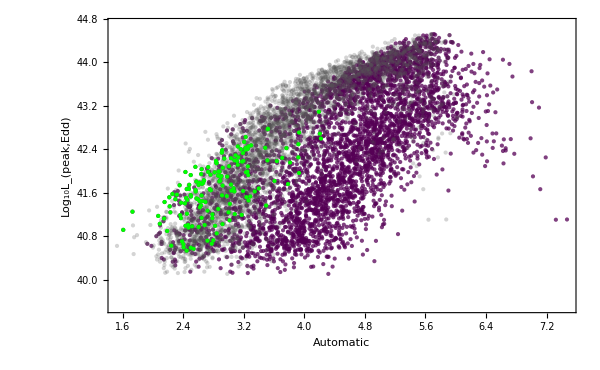

```mathematica
delayconst=1;
wdleddpeakpl=ListPlot[{Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2 Min[#]&/@({medds,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ)}ᵀ],Log10[{yr(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2 Min[#]&/@({medds,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ)}ᵀ],Extract[Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2 Min[#]&/@({medds,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ)}ᵀ],Position[βs,x_/;x>3]]},Axes->False,Frame->True,PlotRange->{All,{39.5,44.7}},ImageSize->600,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{{"Log_10L_(peak,Edd)","Log_10(Ṁ)_(peak,Edd) (M_⊙/yr)"},{Automatic,Automatic}},FrameTicks->{{Automatic,LinTicks[-7,6,1,4,TickPostTransformation->(#+Log10[msun/yr 0.1 c^2]&)]},{Automatic,Automatic}},PlotStyle->{Directive[Darker@Purple,Opacity@0.75],Directive[Darker@Gray,Opacity@0.25],Directive[PointSize@Medium,Green,Opacity@1]},ImagePadding->{{60,60},{0,5}}]
(*wdpl=Grid[{{wdlpeakpl},{wdeddratpl}},Spacings->{0,0}]
Export[nd<>"wd-tpeak-lpeak-eddrat-eddlim.pdf",wdpl];*)
```

10. Tally of which streams collide with which.

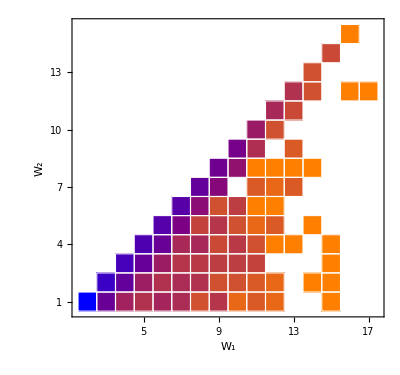
-Graphics- | -Graphics-

```mathematica
(*orbpairtally=Tally@Flatten[collidingstreams⟦All,All,1,{1,2}⟧,1];*)
orbpairtally=Tally@Table[collidingstreams⟦i,circcollind⟦i⟧,1,{1,2}⟧,{i,nexamples}];
maxtally=Max[orbpairtally⟦All,2⟧];
ticksspec=Table[{i,i,{0,0.02}},{i,20}];
lmaxtally=Log10@maxtally;
colorblend={Orange,Purple,Blue};
colorbar=Show[Graphics[Table[{Blend[colorblend,tally/lmaxtally],Rectangle[{0,tally},{1,tally+0.01}]},{tally,0,lmaxtally,0.01}]],AspectRatio->Full,ImageSize->{90,500},Frame->True,PlotRangePadding->0,FrameTicks->{{None,With[{x=Range[0,lmaxtally,0.5]},{x,NumberForm[#,{2,1}]&/@x}ᵀ]},{None,None}},FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],ImagePadding->{{5,55},{60,35}},FrameLabel->{{None,"Log_10N"},{None,None}}];
windingspl=Grid[{{Show[Graphics@Flatten[({Blend[colorblend,(Log10@#⟦2⟧)/(Log10@maxtally)],EdgeForm[White],Rectangle[Reverse@#⟦1⟧-{1/2,1/2}]}&/@orbpairtally)],Frame->True,PlotRangePadding->0,FrameTicks->{{ticksspec,ticksspec},{ticksspec,ticksspec}},FrameStyle->Directive[AbsoluteThickness@1,FontSize->20],ImagePadding->{{60,35},{60,35}},ImageSize->{Automatic,500},FrameLabel->{"W_1","W_2"}],colorbar}},Background->White]
Export[nd<>"windings"<>fsuffix<>".pdf",windingspl];
```

11. Precession angles and t_circ for all realizations.

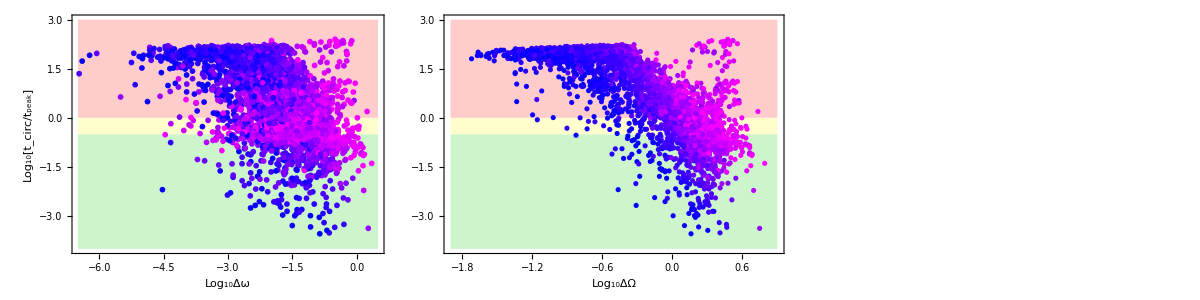

```mathematica
colorbar=Show[Graphics[Table[{Blend[{Blue,Magenta},(mh-5)/(8-5)],Rectangle[{0,mh},{1,mh+0.01}]},{mh,5,7.99,0.01}]],AspectRatio->Full,ImageSize->{90,400},Frame->True,PlotRangePadding->0,FrameTicks->{{None,With[{x=Range[5,8,0.5]},{x,NumberForm[#,{2,1}]&/@x}ᵀ]},{None,None}},FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],ImagePadding->{{10,55},{55,10}},FrameLabel->{{None,"Log_10M_h"},{None,None}}];
precpl=Grid[{{Show[ListPlot[{{{-6.5,-1/2},{0.5,-1/2}},{{-6.5,0},{0.5,0}}},PlotRange->{All,{-4,3}},Joined->True,Axes->False,Filling->{1->{Bottom,Lighter[delaycolors⟦1⟧,0.8]},2->{{1},Lighter[delaycolors⟦2⟧,0.8]},2->{Top,Lighter[delaycolors⟦3⟧,0.8]}},PlotStyle->None],Graphics[{PointSize[0.0075]}~Join~Riffle[(Blend[{Blue,Magenta},(#-5)/(8-5)]&)/@Log10@mhs,Point/@({Log10[(4π aspins)/(c^3 qs^(1/2))((βs G mhs msun)/(2 rss rsun))^(3/2)Abs[Dot[{0,0,1},#]&/@spindirs]],Log10@circratio}ᵀ)]],AspectRatio->Full,ImageSize->{550,400},Frame->True,PlotRangePadding->0,PlotRangeClipping->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{"Log_10Δω","Log_10[t_circ/t_peak]"},ImagePadding->{{55,1},{55,10}},PlotRange->All],Show[ListPlot[{{{-1.9,-1/2},{0.9,-1/2}},{{-1.9,0},{0.9,0}}},PlotRange->{All,{-4,3}},Joined->True,Axes->False,Filling->{1->{Bottom,Lighter[delaycolors⟦1⟧,0.8]},2->{{1},Lighter[delaycolors⟦2⟧,0.8]},2->{Top,Lighter[delaycolors⟦3⟧,0.8]}},PlotStyle->None],Graphics[{PointSize[0.0075]}~Join~Riffle[(Blend[{Blue,Magenta},(#-5)/(8-5)]&)/@Log10@mhs,Point/@({Log10[(6π G mhs msun βs)/(2 c^2 qs^(1/3)rss rsun)],Log10@circratio}ᵀ)]],AspectRatio->Full,ImageSize->{495,400},Frame->True,PlotRangePadding->0,PlotRangeClipping->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{"Log_10ΔΩ",None},ImagePadding->{{0,1},{55,10}}],colorbar}},Spacings->0]
Export[NotebookDirectory[]<>"circ-precession.pdf",precpl];
```